```mathematica
Exit[]
```

## init

```mathematica
Get["/data/mapk/mapk01.mx"];
Get["/home/abergman/dicty/SPSA.m"]
```

```mathematica
LaunchKernels[]
ParallelEvaluate[$KernelID]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local],KernelObject[9,local],KernelObject[10,local],KernelObject[11,local],KernelObject[12,local],KernelObject[13,local],KernelObject[14,local],KernelObject[15,local],KernelObject[16,local]}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

```mathematica
lenX=Range[0.01,1.0,0.05]
Length[lenX]
```

{0.01,0.06,0.11,0.16,0.21,0.26,0.31,0.36,0.41,0.46,0.51,0.56,0.61,0.66,0.71,0.76,0.81,0.86,0.91,0.96}

20

```mathematica
{v,θ0}={{p2, p3a, p3b, p3c, p3d, p4, p5, StotNative, StotOE, maxdose, dX}, {10.0, 0.01, 0.9, 300, 0.005, 1.0, 0.01, 3., 3000, 1, 0.0001}};
```

```mathematica
tend=10000;
pθ:=Thread[Rule[v,θ0]];
slevel:={StotNative,StotOE}
```

## θ_0

### {2013, 1, 10, 12, 4, 4.612945`7.41655326462845}

```mathematica
θ0={56.43622167122431,0.7330821293559258,0.10711435454491272,4.494752156231409,0.,0.33197473798885224,0.02307916714522569,3.236850982008374};
```

### {2013, 1, 10, 16, 55, 13.940242`7.896845298712761}

```mathematica
θ0={56.70995318158104,0.7832247267456027,0.09889924756473911,5.292187714746446,0.000018875209270420096,0.3404435189016253,0.023315554320830257,3.231950927247027,8000,1};
```

### {2013, 2, 1, 15, 58, 56.982145`8.508313767405074}

```mathematica
θ0={56.7,0.78,0.099,5.29,0.00001887,0.34,2.3,3.2,8000,0.003,0.0001};
```

### {2013, 2, 5, 2, 19, 10.254256`7.763479141939724}

```mathematica
θ0={52.21735991847011,0.6612387910017867,0.10539118677976374,6.804287711804248,0.00003251897413491861,0.29275450884588866,2.546839611203239,5.033807222328056,37.53025448849591,0.0020079676418921387};
```

### {2013, 2, 13, 15, 50, 30.059483`8.230556487761254}

```mathematica
θ0={39.935231497016815,0.6440733655347445,0.03887780263284455,6.480113948617697,0.000024878875411436162,0.11540533470205612,2.9043056225369415,3.8220042675376393,8752.224246002497,0.0012566523292079355,0.00006429946675391224}
```

{39.9352,0.644073,0.0388778,6.48011,0.0000248789,0.115405,2.90431,3.822,8752.22,0.00125665,0.0000642995}

```mathematica
Print/@SetPrecision[θ0,3]
```

## Plots

```mathematica
Grid[List@@#&/@pθ//Transpose,Frame->All]
```

p2 | p3a | p3b | p3c | p3d | p4 | p5 | StotNative | StotOE | maxdose | dX
7.63831 | 0.64 | 0.381033 | 6.48 | 0.000025 | -6.64935×10^-8 | 34.8912 | 0.07185 | 0.651285 | 0.00384417 | 0.000064

### Uniform stim, no transport inhibition

```mathematica
dat=Transpose@ParallelTable[
plist=Join[{δ->maxdose*l,Stot->s,p1[_]->p5*maxdose*l,p3[_]->p3b}/.pθ,pθ];
runsim[plist]
,{l,lenX},{s,slevel/.pθ},Method->"FinestGrained"];
Dimensions[dat]
```

{2,20,67}

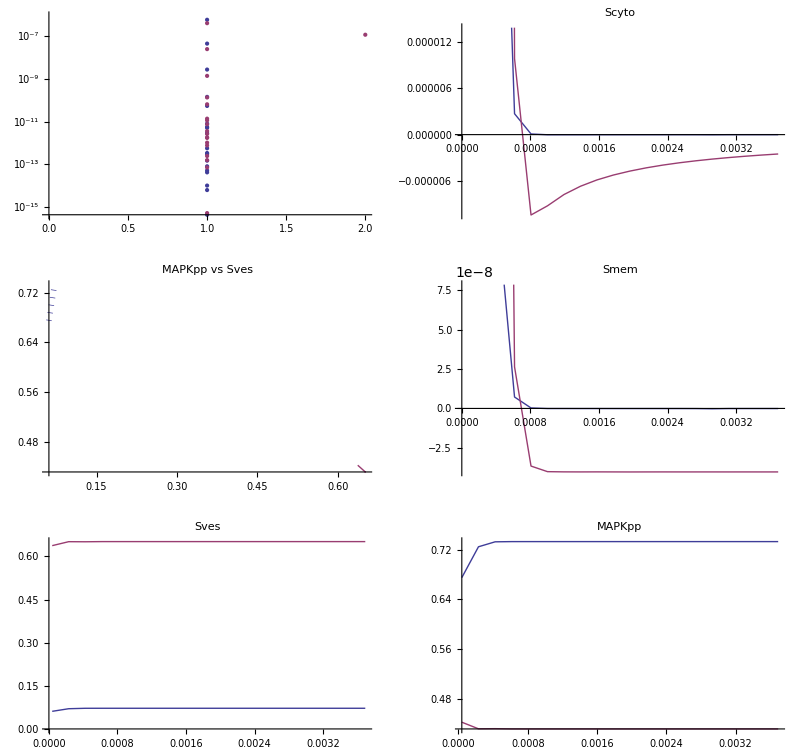

```mathematica
GraphicsGrid[{
{ListLogPlot[{runsim$maxiter,dd}/.dat],ListLinePlot[{δ,Scyto[0]}/.dat,PlotLabel->"Scyto"]},
{
ListLinePlot[{(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0]),MAPKpp[0]/MAXMAPKPP}/.dat,PlotLabel->"MAPKpp vs Sves",PlotStyle->{{Dotted,Thickness[0.01]},Thick},PlotRange->All,AxesLabel->{}],
ListLinePlot[{δ,Smem[0]}/.dat,PlotLabel->"Smem"]
},{
ListLinePlot[{δ,(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])}/.dat,PlotLabel->"Sves"],
ListLinePlot[{δ,MAPKpp[0]/MAXMAPKPP}/.dat,PlotLabel->"MAPKpp",PlotRange->All]
}},ImageSize->Full]
```

### Uniform stim, Transport Inhibition

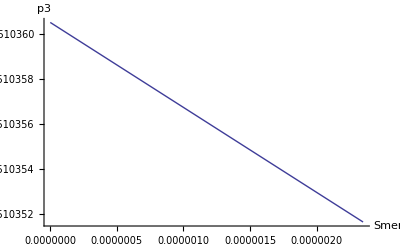

```mathematica
p3sigmoid=Function[s,p3[s]->(p3b-p3d)/(1+Exp[p3c(Smem[s][t]-p3a)])+p3d]/@{0,1};
Plot[p3[0]/.p3sigmoid/.pθ/.Smem[0][t]->Smem//Evaluate,{Smem,0,Max[Smem[0]/.dat]},PlotRange->{p3b/.pθ,0},AxesLabel->{"Smem","p3"}]
```

```mathematica
dat=Transpose@ParallelTable[
plist=Join[{δ->l*maxdose,Stot->s,p1[_]->p5*l*maxdose,p3sigmoid}/.pθ,pθ];
runsim[plist]
,{l,lenX},{s,slevel/.pθ},Method->"FinestGrained"];
Dimensions[dat]
```

{2,20,68}

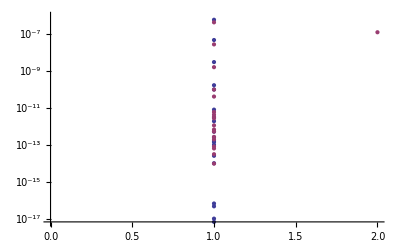

```mathematica
{runsim$maxiter,dd}/.dat//ListLogPlot
```

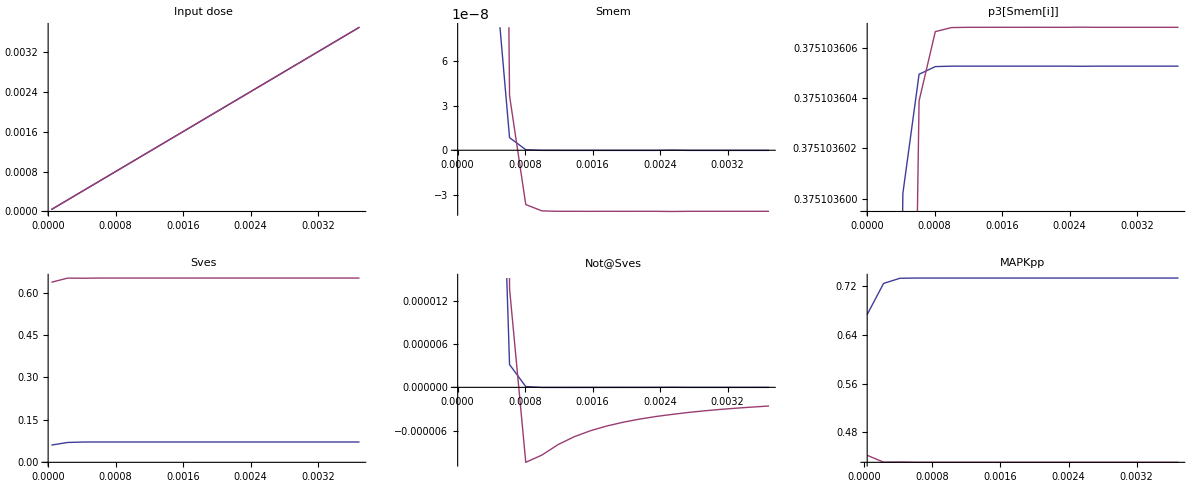

```mathematica
GraphicsGrid[{
{ListLinePlot[{δ,δ}/.dat,PlotLabel->"Input dose"],
ListLinePlot[{δ,Smem[0]}/.dat,PlotLabel->"Smem"],
ListLinePlot[{δ,p3[0]}//.(dat/.x_[t]->x),PlotLabel->"p3[Smem[i]]"]},
{ListLinePlot[{δ,(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])}/.dat,PlotLabel->"Sves"],
ListLinePlot[{δ,Stot-(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])}/.dat,PlotLabel->"Not@Sves"],
ListLinePlot[{δ,MAPKpp[0]/MAXMAPKPP}/.dat,PlotRange->All,PlotLabel->"MAPKpp"]}
},ImageSize->Full]
```

### Gradient stim

{2,20,70}

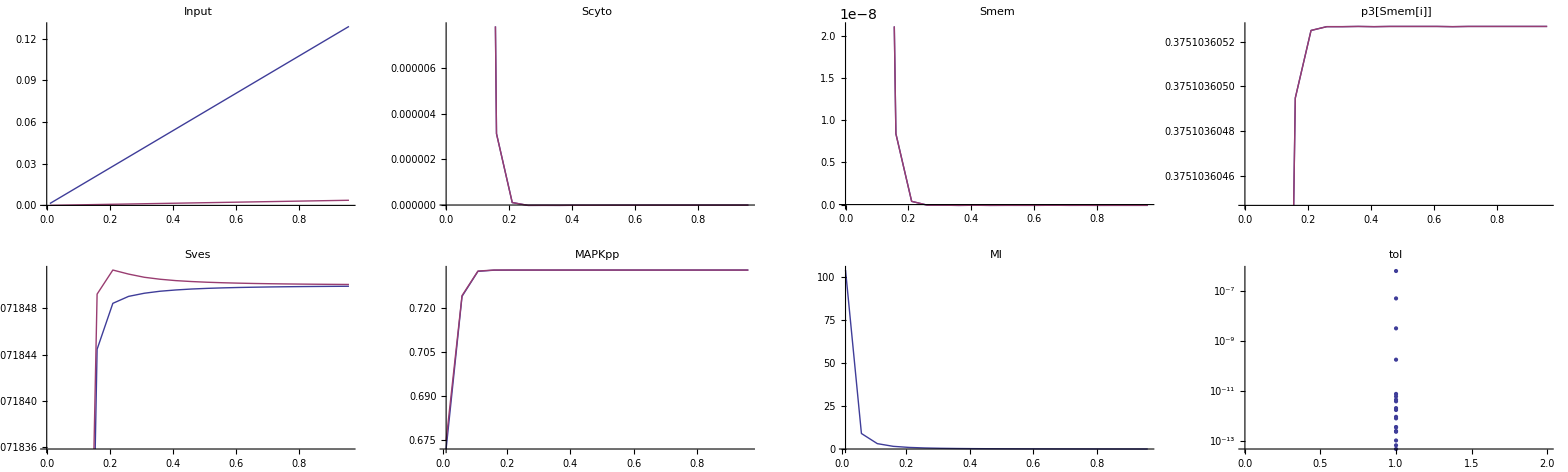

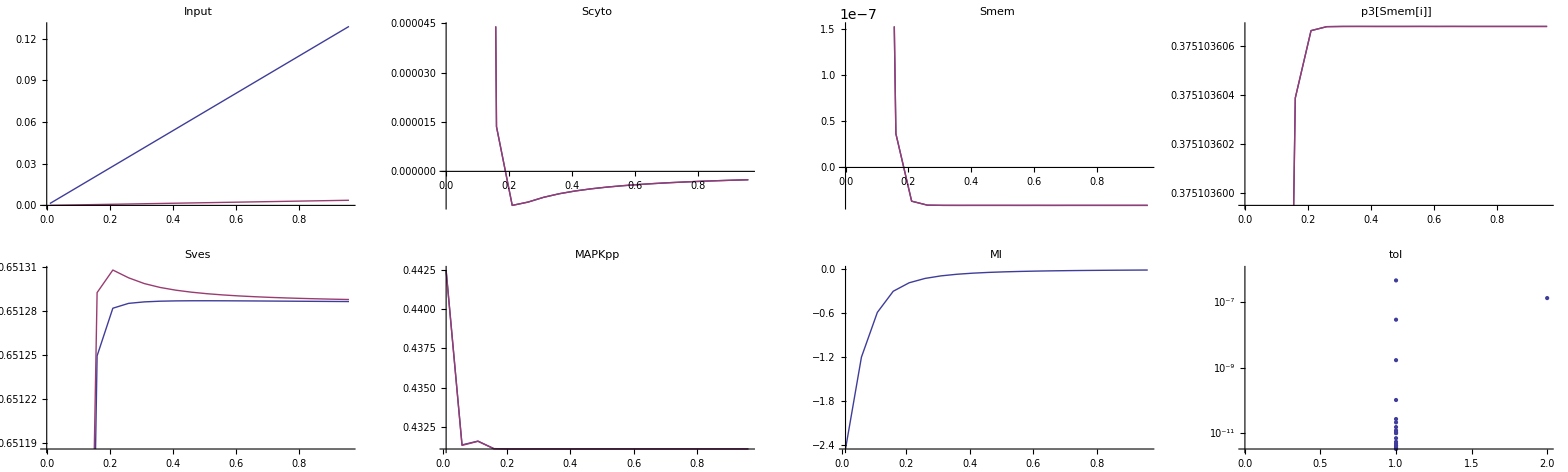

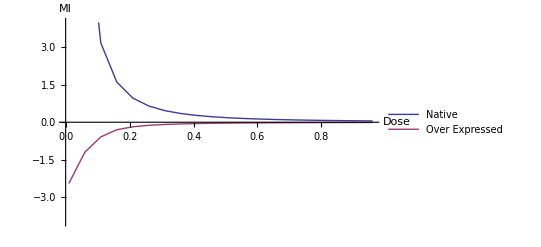

```mathematica
dat=Transpose@ParallelTable[
plist=Join[{δ->l,Stot->s,p1[0]->p5*l*maxdose,p1[1]->p5*maxdose(l+dX),p3sigmoid,Di->0.0001}/.pθ,pθ];
runsim[plist]
,{l,lenX},{s,slevel/.pθ},Method->"FinestGrained"];
Dimensions[dat]
gf=Function[dat,
GraphicsGrid[{{
ListLinePlot[{{δ,p1[0]},{δ,p1[1]/p5}}/.dat//Transpose,PlotLabel->"Input"],
ListLinePlot[{{δ,Scyto[0]},{δ,Scyto[1]}}/.dat//Transpose,PlotLabel->"Scyto"],
ListLinePlot[{{δ,Smem[0]},{δ,Smem[1]}}/.dat//Transpose,PlotLabel->"Smem"],
ListLinePlot[{{δ,p3[0]},{δ,p3[1]}}//.dat/.x_[t]->x//Transpose,PlotLabel->"p3[Smem[i]]"]
},{
ListLinePlot[{
{δ,(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0])},
{δ,(C1[1]+C2[1]+C3[1]+C4[1]+C5[1]+C6[1]+C7[1]+C8[1]+C9[1])}
}/.dat//Transpose,PlotLabel->"Sves"],
ListLinePlot[{{δ,MAPKpp[0]/MAXMAPKPP},{δ,MAPKpp[1]/MAXMAPKPP}}/.dat//Transpose,PlotRange->All,PlotLabel->"MAPKpp"],
ListLinePlot[{δ,(MAPKpp[1]-MAPKpp[0])/(dX*maxdose)}/.dat,PlotRange->All,PlotLabel->"MI"],
ListLogPlot[{runsim$maxiter,dd}/.dat,PlotLabel->"tol"]
}},ImageSize->Full]];
gf[dat[[1]]]
gf[dat[[2]]]
ListLinePlot[{δ,(MAPKpp[1]-MAPKpp[0])/(dX*maxdose)}/.dat,PlotRange->.4{-1,1}10^1,AxesLabel->{"Dose","MI"},PlotLegends->LineLegend[{"Native","Over Expressed"}]]
```

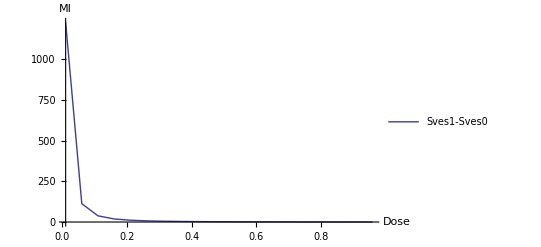

```mathematica
ListLinePlot[{δ,1/(dX*maxdose)((C1[1]+C2[1]+C3[1]+C4[1]+C5[1]+C6[1]+C7[1]+C8[1]+C9[1])-(C1[0]+C2[0]+C3[0]+C4[0]+C5[0]+C6[0]+C7[0]+C8[0]+C9[0]))}/.dat[[1]],PlotRange->All,AxesLabel->{"Dose","MI"},PlotLegends->LineLegend[{"Sves1-Sves0","Over Expressed"}]]
```

### MI-MAPK vs Stot

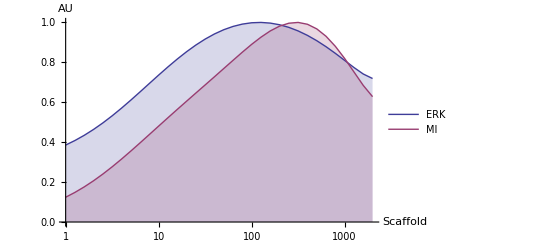

```mathematica
Block[{MI,ERK,dat},
dat=Transpose@ParallelTable[
plist=Join[{δ->l,Stot->10^s,p1[0]->p5*l*maxdose,p1[1]->p5*maxdose(l+dX),p3sigmoid,Di->0.0001}/.pθ,pθ];
runsim[plist]
,{l,lenX},Evaluate[Flatten[{s,Log[10,slevel],.1}]/.pθ],Method->"FinestGrained",DistributedContexts->None];
ERK={Stot/StotNative,(MAPKpp[0]+MAPKpp[1])/2}/.dat//Transpose//Mean;
MI={Stot/StotNative,MAPKpp[1]-MAPKpp[0]}/.dat//Transpose//Mean;
ListLogLinearPlot[{ERKᵀ/{1,Max[ERK[[All,2]]]}//Transpose,MIᵀ/{1,Max[MI[[All,2]]]}//Transpose},Joined->True,Filling->Axis,AxesLabel->{"Scaffold","AU"},PlotStyle->Thick,PlotLegends->LineLegend[{"ERK","MI"}]
]
]
```

### MI vs grad

```mathematica
grad=Range[0.0,1.0,0.25]
Length[grad]
```

{0.,0.375,0.75,1.125,1.5}

5

```mathematica
inputs0=Flatten@Outer[Times,X,grad];
inputs1=Flatten@Outer[Times,X+dX,grad];
```

```mathematica
(inputs1-inputs0)/dX//ListPlot
```

```mathematica
Block[{dat, MI,pr={0,0.02}},
dat=Table[
dat=ParallelTable[
plist=Flatten@Join[{Stot->s,p1[0]->p5*inputs0[[d]],p1[1]->p5*inputs1[[d]],p3sigmoid,Di->0.0001}/.pθ,pθ];
runsim[plist]
,{d,Length@inputs0}];
Partition[dat,Length[grad]]
,{s,slevel}];

MI=MAPKpp[1]-MAPKpp[0]/.dat;

GraphicsGrid[{
{ListLinePlot[(Transpose@MI[[1]])/dX,PlotRange->pr],ListLinePlot[(Transpose@MI[[2]])/dX,PlotRange->pr]},
{ListLinePlot[Map[{grad,#}ᵀ&,Mean[MAPKpp[1]-MAPKpp[0]/.Transpose@dat]],PlotMarkers->Automatic,PlotLegends->LineLegend[{"Native","Overexpressed"}],AxesLabel->{"Gradient","MI"},PlotRange->10^-5{-3,4}]}
}]]
```

## Optimization

### Loss

```mathematica
Loss[θ_?(VectorQ[#,NumericQ]&)]:=With[{pθ=Thread[v->Abs@θ]},
dat=Transpose@ParallelTable[
plist=Join[{δ->l,Stot->s,p1[0]->p5*l*maxdose,p1[1]->p5*maxdose(l+dX),p3sigmoid,Di->0.0001}/.pθ,pθ];
runsim[plist]
,{l,lenX},{s,slevel/.pθ},Method->"FinestGrained",DistributedContexts->None];

{MIsimNative,MIsimOE}={δ,(MAPKpp[1]-MAPKpp[0])/(dX*maxdose)}/.dat;
MIsimOE=Select[MIsimOE,#[[1]]>0.1&];
equNative=Fit[MIsimNative,{1,x},x];
equOE=Fit[MIsimOE,{1,x},x];
MIerrorNative=Mean@Abs[MIsimNative[[All,2]]-(equNative/.x->lenX)];
MIerrorOE=Mean@Abs[MIsimOE[[All,2]]-(equOE/.x->MIsimOE[[All,1]])];

lossfuncs=Hold[
(StotOE/StotNative-9)^2/.pθ,
Mean[(MAPKpp[0]+MAPKpp[1])/2/.Last@dat],
MIerrorNative,
MIerrorOE,
equNative/.a_+b_*x->(a-2)^2,
equNative/.a_+b_*x->b^2,
(x-0.8)^2/.Solve[equNative==equOE][[1]],
(x-0.2)^2/.Solve[equOE==0][[1]]
];
lossfuncsexp=List@@Map[Defer,lossfuncs];
lossfuncsval={ReleaseHold[lossfuncs]};

w.lossfuncsval
]
Loss[θ0]
```

w.{5.20276×10^6,0.00615659,0.0242671,0.379519,0.269949,0.981975,0.00537938,0.184244}

```mathematica
Loss[θ0]
```

3.23565

```mathematica
sol[[-1]]
```

{3.61514,{63.2302,0.865525,0.097131,6.04054,0.00328151,0.345737,0.0113781,40.265,6856.06}}

```mathematica
Loss[sol[[1,2]]]
```

18.7492

```mathematica
Dynamic[BarChart[w lossfuncsval,BarOrigin->Left,ChartLabels->lossfuncsexp,PlotRange->{{-2,2},All}]]
```

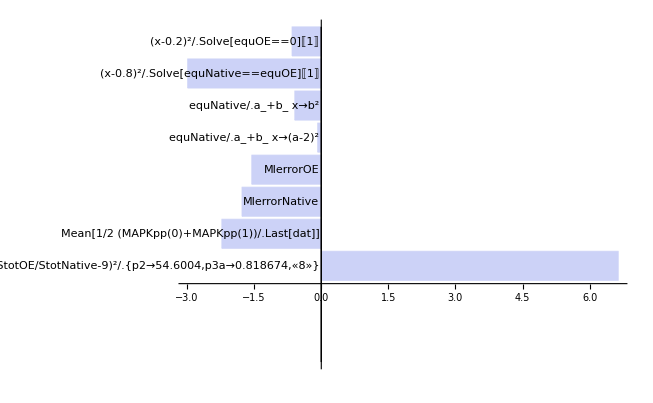

```mathematica
BarChart[Log[10,lossfuncsval],BarOrigin->Left,ChartLabels->(Shallow[#,{8,2}]&/@lossfuncsexp)]
```

```mathematica
w=1/lossfuncsval
```

{1.92206×10^-7,162.427,41.2081,2.63492,3.70441,1.01836,185.895,5.42759}

```mathematica
w={1.6115825079479222*^-7,165.90774899794874,7.399900768321433,2.0376045211887734,0.9120659516298906,6.436712827249171,9301.228238383987,5.0632679873308994}
```

{1.61158×10^-7,165.908,7.3999,2.0376,0.912066,6.43671,9301.23,5.06327}

```mathematica
lossfuncsval
```

{2.83343×10^6,0.0076667,0.0753734,57.7031,1.73138,0.0641041,0.00214558,0.114772}

```mathematica
w=Array[1&,Length[lossfuncs]]
w=w/Norm[w,1.];
```

{1,1,1,1,1,1,1,1}

```mathematica
{Range[Length[w]],
Table[With[{i=i},InputField[Dynamic[w[[i]]],Number,FieldSize->{4,1}]],{i,1,Length[w]}],
Table[With[{i=i},Dynamic[ScientificForm@SetPrecision[lossfuncsval[[i]],3]]],{i,1,Length[w]}],
Table[With[{i=i},Dynamic[lossfuncsval[[i]]w[[i]]]],{i,1,Length[w]}],
lossfuncsexp}ᵀ//TableForm[#,TableHeadings->{None,{"i","w","val","w.v","exp"}}]&
```

### FD

```mathematica
δp=0.01;
grad=FDGradientP[Loss,θ0,δp]
```

{0.381002,28.9744,294.23,-1.19789,-41027.9,-74.5602,-5.55629,4.35581,-0.00370399,-23731.2,2953.5}

```mathematica
Loss[θ0]//ScientificForm
```

8.

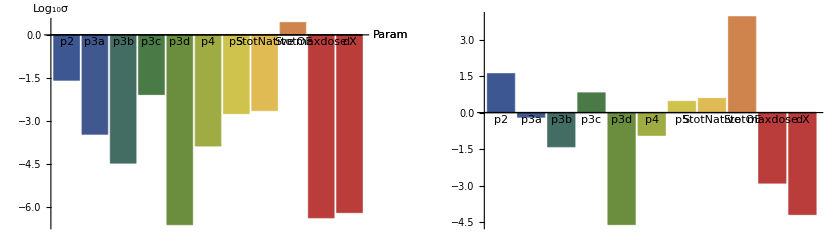

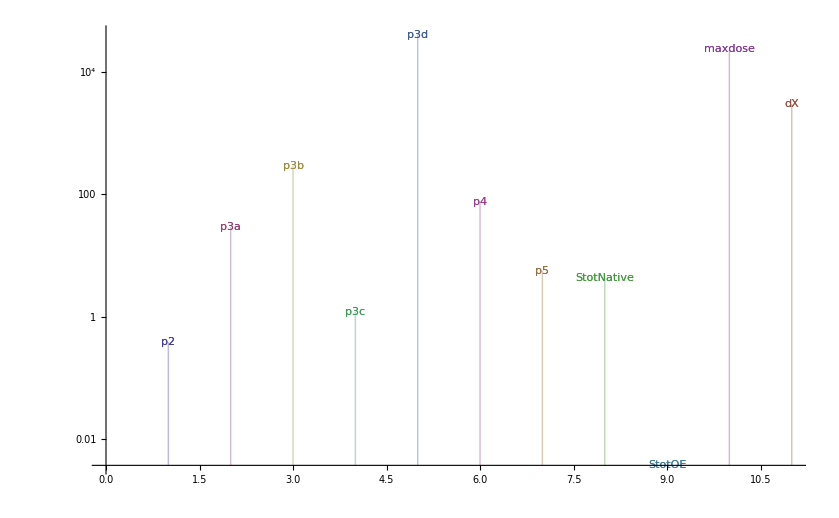

```mathematica
δL=10^-2;
σ0=δL/Abs@grad;
σ0=σ0/.ComplexInfinity->100;
σ0=MapThread[Function[{p,s},Clip[s,{0.,δp*p}]],{θ0,σ0}];
GraphicsRow[{
BarChart[Log[10,σ0],ChartLabels->v,ChartStyle->"DarkRainbow",AxesLabel->{"Param","Log_10σ"}],
BarChart[Log[10,θ0],ChartLabels->v,ChartStyle->"DarkRainbow"]}]
ListLogPlot[{Array[{#,Abs@grad[[#]]}&,Length[grad]]}ᵀ,PlotRange->All,Filling->Bottom,PlotMarkers->v]
```

```mathematica
TableForm[{θ0,δp θ0,σ0,grad}//SetPrecision[#,2]&,TableHeadings->{{"θ0","δp.θ0","σ0","grad"},v}]
```

| p2 | p3a | p3b | p3c | p3d | p4 | p5 | StotNative | StotOE | maxdose | dX
θ0 | 40. | 0.75 | 0.038 | 5.8 | 0.000025 | 0.12 | 2.8 | 3.7 | 7900. | 0.0016 | 0.000065
δp.θ0 | 0.4 | 0.0075 | 0.00038 | 0.058 | 2.5×10^-7 | 0.0012 | 0.028 | 0.037 | 79. | 0.000016 | 6.5×10^-7
σ0 | 0.052 | 0.0045 | 0.000078 | 0.052 | 2.5×10^-7 | 0.000024 | 0.0037 | 0.006 | 48. | 5.4×10^-6 | 6.5×10^-7
grad | 0.19 | 2.2 | -130. | -0.19 | -4700. | 410. | -2.7 | -1.7 | -0.00021 | 1800. | -2000.

### Opt

```mathematica
sol=.
```

{39.9352,0.644073,0.0388778,6.48011,0.0000248789,0.115405,2.90431,3.822,8752.22,0.00125665,0.0000642995}

5.721

Take::take: Cannot take positions -100000 through -1 in {8., 7.99639, 7.99639, 7.99639, 7.99084, 7.98861, 7.98861, 7.98861, 7.98861, 7.98861, 7.98861, 7.98861, « 27 », 7.98336, 7.98336, 7.98336, 7.98336, 7.98336, 7.98336, 7.98336, 7.98336, 7.98336, 7.98336, 7.98336, « 14654 »}.

Fit::fitd: First argument Log[Take[{8., 7.99639, 7.99639, 7.99639, 7.99084, 7.98861, 7.98861, 7.98861, 7.98861, 7.98861, 7.98861, 7.98861, « 28 », 7.98336, 7.98336, 7.98336, 7.98336, 7.98336, 7.98336, 7.98336, 7.98336, 7.98336, 7.98336, « 14654 »}, -100000]] in Fit is not a list or a rectangular array.

«1»

General::ivar: 1.30036 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

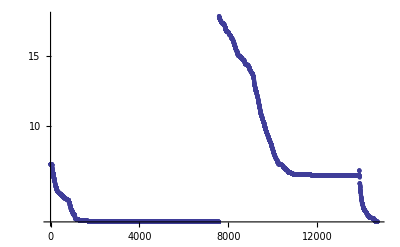

Fit::fitd: First argument Log[Take[{8., 7.99639, 7.99639, 7.99639, 7.99084, 7.98861, 7.98861, 7.98861, 7.98861, 7.98861, 7.98861, 7.98861, « 28 », 7.98336, 7.98336, 7.98336, 7.98336, 7.98336, 7.98336, 7.98336, 7.98336, 7.98336, 7.98336, « 14654 »}, -100000]] in Fit is not a list or a rectangular array.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Fit[Log[Take[{8.,7.99638755888011,7.99638755888011,7.99638755888011,«14697»,5.72100342010264,5.72100342010264,5.72100342010264},-100000]],{1,x},x]→-«19»}}

```mathematica
MyConstraints=Clip[#1,{0.0,50000}]&;
SPSAConstraints[MyConstraints];
SPSAMaxEvals[1*10^5]
sol=If[Head[sol]===List,
sol~Join~RandomSearch[Loss,θ0,σ0],
RandomSearch[Loss,θ0,σ0]
];
θ0=sol[[-1,2]]
Loss[θ0]
lossfit=Fit[Log@Take[sol[[All,1]],-SPSA`Private`MaxEvaluations],{1,x},x]
Show[
ListLogPlot[sol[[All,1]],PlotRange->All],
LogPlot[Exp[lossfit],{x,1,Length[sol]}]]
Solve[Exp[lossfit]==0.1*sol[[-1,1]]]
```

```mathematica
θ0
```

{29.7407,0.500357,0.0284162,9.41987,0.0000173898,0.11254,1.87704,3.73036,1829.08,0.00592189}

```mathematica
Loss[θ0]
```

1.87044

```mathematica
Dynamic[Show[
ListLinePlot[{δ,(MAPKpp[1]-MAPKpp[0])/(dX*maxdose)}/.dat,PlotRange->3*10^0{-1,1},AxesLabel->{"Dose","MI"},PlotLegends->LineLegend[{"Native","Over Expressed"}]],
Plot[{equNative,equOE},{x,0,1}]
]]
```

```mathematica
sol[[-1]]
```

{4.50326,{56.5561,0.819883,0.0334152,5.44799,0.0000197074,0.115981,2.30165,6.01025,247.641,0.00299877}}

```mathematica
θ0=sol[[-1,2]]
```

{57.1524,0.804858,0.0979812,4.61618,0.00729145,0.343103,0.0233002,4.72229,7753.27}

```mathematica
θ0=sol[[1,2]];
```

```mathematica
sol=θ0;
θ0=sol[[-1,2]]
```

{56.4362,0.733082,0.107114,4.49475,0.,0.331975,0.0230792,3.23685}

```mathematica
Loss[Last@sol[[1]]]
```

0.00143693

```mathematica
Loss[Last@sol[[-1]]]
```

0.00144529

```mathematica
GraphicsGrid[MapThread[Function[{v,p},ListLogPlot[p,PlotLabel->ToString[v],PlotRange->All]],{v,sol[[All,2]]ᵀ}]//Partition[#,3,3,1]&,ImageSize->Full]
```

```mathematica
sol[[-1]]
```

{2.04596,{62.7853,0.817014,0.0989842,5.42613,0.0067144,0.33634,0.0108079,9.96061,6872.65}}

```mathematica
Loss[sol[[-1,2]]]
```

5.84289

```mathematica
ListLinePlot[sol[[All,1]]]
```

```mathematica
datestr=ToString[AbsoluteTime[Round@Date[]]-AbsoluteTime[{2013,1,1,0,0,0}]]
solfilename="/data/mapk/sol."<>datestr<>".mx"
DumpSave["/data/mapk/sol."<>datestr<>".mx",sol];
```

3587564

/data/mapk/sol.3587564.mx

```mathematica
Block[{files=FileNames["/data/mapk/sol.*.mx"]},
Print@TableForm[files];
Get@Last@files;
Last[sol]
]
```

/data/mapk/sol.1775542.mx
/data/mapk/sol.2550694.mx
/data/mapk/sol.2635972.mx
/data/mapk/sol.2649741.mx
/data/mapk/sol.2725469.mx
/data/mapk/sol.2976423.mx
/data/mapk/sol.3013667.mx
/data/mapk/sol.3014419.mx
/data/mapk/sol.3015189.mx
/data/mapk/sol.3236506.mx
/data/mapk/sol.3255267.mx
/data/mapk/sol.3256037.mx
/data/mapk/sol.3271594.mx
/data/mapk/sol.3323956.mx

{24.9369,{31.4682,0.601645,0.0261638,7.09911,0.0000105394,0.0700033,1.76226,3.45063,3102.25,0.00434795}}

```mathematica
θ0
```

{31.4682,0.601645,0.0261638,7.09911,0.0000105394,0.0700033,1.76226,3.45063,3102.25,0.00434795}

```mathematica
{lossval,θ0}=sol[[-1]]
```

{24.9369,{31.4682,0.601645,0.0261638,7.09911,0.0000105394,0.0700033,1.76226,3.45063,3102.25,0.00434795}}

```mathematica
Loss[θ0]
```

Loss[{31.4682,0.601645,0.0261638,7.09911,0.0000105394,0.0700033,1.76226,3.45063,3102.25,0.00434795}]

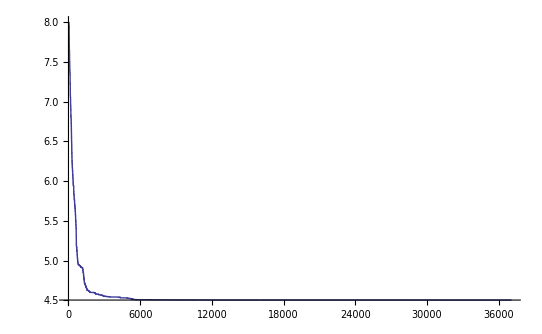

```mathematica
ListLinePlot[sol[[All,1]],PlotRange->All]
```